```mathematica
(*Алгоритм Форда-Беллмана с визуализацией результата*)
```

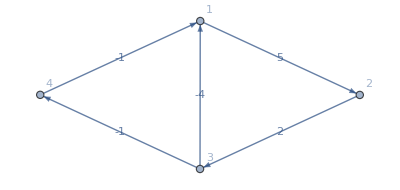

```mathematica
edges={1->2,2->3,3->1,4->1,3->4};
edgeWeights={5,2,-4,-1,-1};
g=Graph[edges,EdgeWeight->edgeWeights,EdgeLabels->Table[edges⟦i⟧->edgeWeights⟦i⟧,{i,Length[edges]}],VertexLabels->"Name"];
Print[g];
```

```mathematica
targetVertex=2;
pathF=FindShortestPath[g,targetVertex,Method->"BellmanFord"];
Do[Print[targetVertex," -> ",i];Print[pathF[i]];Print[HighlightGraph[g,PathGraph[pathF[i],DirectedEdges->True]]];Print["----------------------"],{i,VertexCount[g]}];
```

2 -> 1

{2,3,1}

-Graphics-

----------------------

2 -> 2

{2}

-Graphics-

----------------------

2 -> 3

{2,3}

-Graphics-

----------------------

2 -> 4

{2,3,4}

-Graphics-

----------------------

```mathematica
(*Алгоритм Флойда-Уоршелла с визуализацией результата*)
```

```mathematica
edges={1->2,2->3,3->1,4->1,3->4};
edgeWeights={5,2,-4,-1,-1};
g=Graph[edges,EdgeWeight->edgeWeights,EdgeLabels->Table[edges⟦i⟧->edgeWeights⟦i⟧,{i,Length[edges]}],VertexLabels->"Name"];
Print[g];
```

-Graphics-

(0. | 5. | 7. | 6.
-2. | 0. | 2. | 1.
-4. | 1. | 0. | -1.
-1. | 4. | 6. | 0.)

1 -> 1

{1}

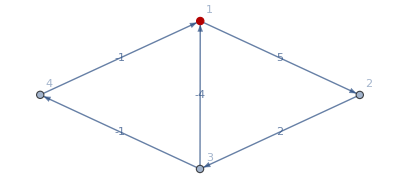

----------------------

1 -> 2

{1,2}

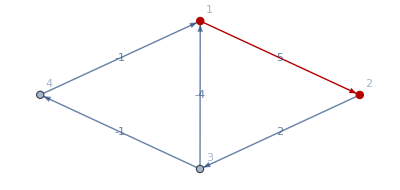

----------------------

1 -> 3

{1,2,3}

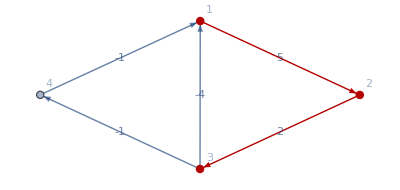

----------------------

1 -> 4

{1,2,3,4}

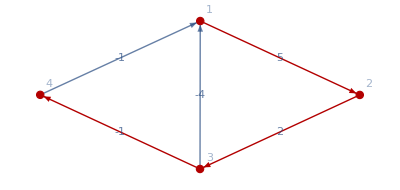

----------------------

2 -> 1

{2,3,1}

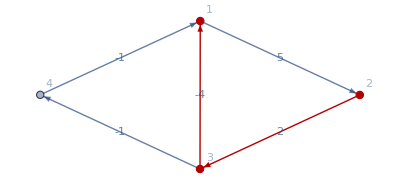

----------------------

2 -> 2

{2}

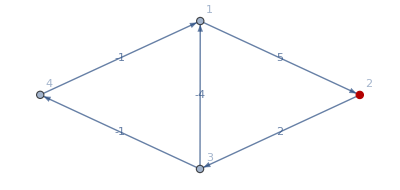

----------------------

2 -> 3

{2,3}

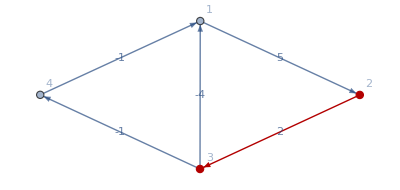

----------------------

2 -> 4

{2,3,4}

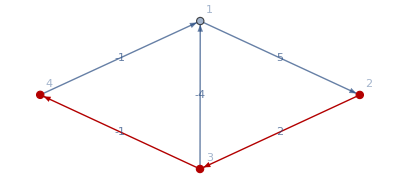

----------------------

3 -> 1

{3,1}

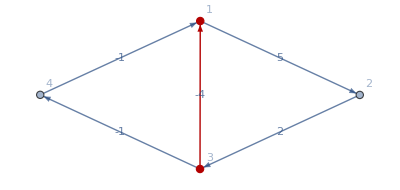

----------------------

3 -> 2

{3,1,2}

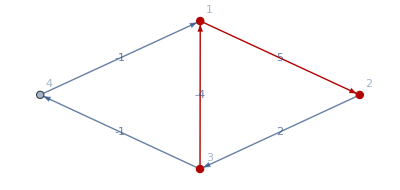

----------------------

3 -> 3

{3}

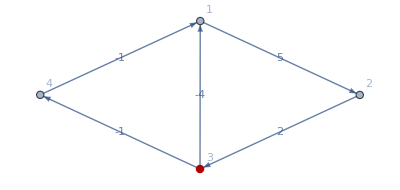

----------------------

3 -> 4

{3,4}

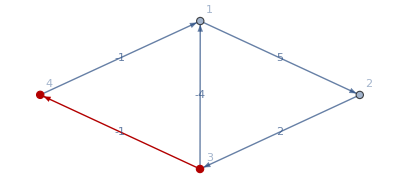

----------------------

4 -> 1

{4,1}

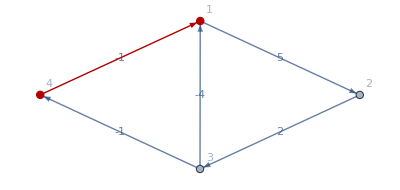

----------------------

4 -> 2

{4,1,2}

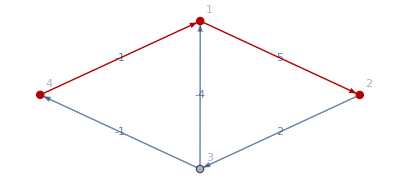

----------------------

4 -> 3

{4,1,2,3}

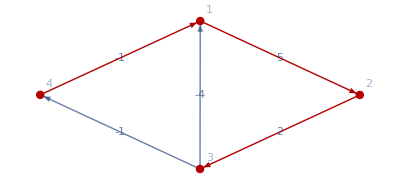

----------------------

4 -> 4

{4}

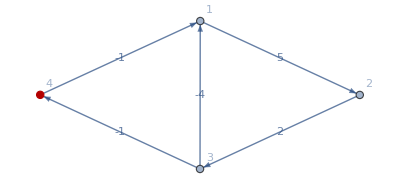

----------------------

```mathematica
M=GraphDistanceMatrix[g,Method->"FloydWarshall"];
pathF=FindShortestPath[g];
Print[MatrixForm[M]];
Do[Print[i," -> ",j];Print[pathF[i,j]];Print[HighlightGraph[g,PathGraph[pathF[i,j],DirectedEdges->True]]];Print["----------------------"],{i,VertexCount[g]},{j,VertexCount[g]}];
```